```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mub={0,50,100,150,200,250,300,350,400,450,500,550,600,650,700};
fitdata=Table[Import["./mub"<>ToString[mub[[i]]]<>".dat"],{i,1,Length[mub]}];
```

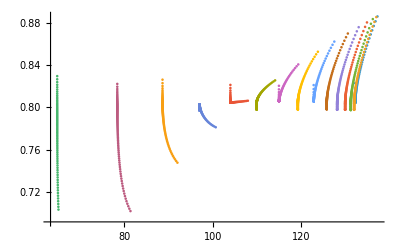

```mathematica
ListPlot[fitdata,PlotRange->All]
```

```mathematica
fitfun=Table[Interpolation[fitdata[[i]]],{i,1,Length[mub]}];
```

```mathematica
Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-0.8)/0.8]==0.1,{x,fitdata[[i]][[1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
```

InterpolatingFunction::dmval: 输入值 {132.151} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {132.152} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

{132.151,131.9,131.142,129.868,128.064,125.705,122.76,119.183,114.916,109.876,103.947,111.733,88.6156,78.3959,64.8266}

```mathematica
Export["nuregion.dat",%]
```

nuregion.dat

```mathematica
Export["mub2.dat",mub]
```

mub2.dat